```mathematica
(* https://github.com/shahin-mansouri *)
```

```mathematica
f[x_, y_]= (1+2y)/x;
x[0] = 1;
y[0] = 0;
xStop = 1.4;
steps = 100;
h = (xStop - x[0])/steps
```

0.004

```mathematica
n = 0;
While[x[n] < xStop,
n = n + 1;
x[n] = x[n-1] + h;
y[n] = NSolve[y[n-1]+h/2(f[x[n-1], y[n-1]] + f[x[n-1], y])-y][[1, 1, 2]]
]
```

```mathematica
x = Table[x[i], {i, 0, n}];
```

```mathematica
y = Table[y[i], {i, 0, n}];
```

```mathematica
xy = Table[{x[i], y[i]}, {i, 0, n}]
```

{{y[x]→InterpolatingFunction[…][x]}}

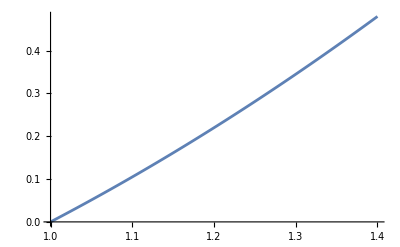

```mathematica
p2 = NDSolve[{ x y'[x] - 2y[x] == 1,y[1]==0}, y[x], {x, 1, 1.4}]
Plot[y[x]/.p2, {x, 1, 1.4}]
```

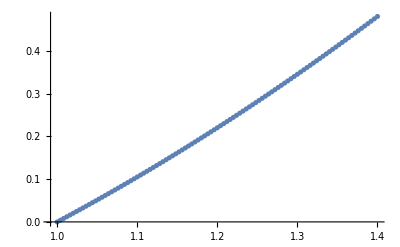

```mathematica
ListPlot[xy]
```